```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
T1[t_]:= t*IdentityMatrix[10]
```

```mathematica
T[t_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=t*IdentityMatrix[m];MAT]
```

```mathematica
Clear[LEFT]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardul/PhD_new/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,3,0.01]}]
```

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+01]]](*Module[{J=Inverse[β[ω,0.0001,1,0,m]],A:=Inverse[β[ω,0.0001,1,0,m]],T:=T1[1]},Do[J=Inverse[IdentityMatrix[m]-A.T.J.T].A,50000];J=J]*)
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
dist[total_,concentration_,area_]:=dist[total,concentration,area]=Table[SortBy[Join[RandomSample[Join[s[1,100,1,area]],concentration],RandomSample[Join[s[1,100,50-area+1,50]],total-concentration]],First],10000]
```

```mathematica
TLD[t_]:=Module[{sizeoflead=10},Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,Table[{a,a},{a,1,sizeoflead}]->t]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,50]]
```

```mathematica
SLLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
SRLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
device1[ω_,sizeoflead_]:=Module[{},Inverse[IdentityMatrix[50]-g[ω,0.0001,1,0].T[1,sizeoflead].SLLEAD[ω,sizeoflead].T[1,sizeoflead]].g[ω,0.0001,1,0]]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,total_,concentration_,number_,size_,area_]:= Module[{sizeoflead=10},
recurs=Module[{J1= device1[ω,sizeoflead]},
Do[
J1=Inverse[IdentityMatrix[50]-Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[dist[total,concentration,area][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[total,concentration,area][[number]][[loc1,2]],dist[total,concentration,area][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]].T[1,50].J1.T[1,50]].Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[dist[total,concentration,area][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[total,concentration,area][[number]][[loc1,2]],dist[total,concentration,area][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]],{unitcell,size}];J1=J1];ir=Inverse[IdentityMatrix[50]-SRLEAD[ω,sizeoflead].TLD[1].recurs.TLD[1]].SRLEAD[ω,sizeoflead];il=Inverse[IdentityMatrix[50]-recurs.TLD[1].SRLEAD[ω,sizeoflead].TLD[1]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1].recurs;
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[1].grr1.TLD[1]-TLD[1].GNON1.TLD[1].GNON1]];If[TRA>10,10,TRA]]
```

```mathematica
input= Monitor[Table[ParallelTable[{ω,CA[ω,0.0001,1,0,1,100,35,n,100,10]},{ω,Range[0,2,0.01]}],{n,50}],n]
```

{{{0.,1.74108},{0.01,0.524964},{0.02,0.319126},{0.03,1.77403},{0.04,0.315855},{0.05,2.74979},{0.06,1.31727},188,{1.95,1.95027},{1.96,2.0705},{1.97,2.6361},{1.98,2.14919},{1.99,2.35618},{2.,2.06533}},48,{1}}
 |  |  |  |

```mathematica
transmission[area_]:=transmission[area]= Table[{x,Import["~/PhD_new/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/size_"<>ToString[area]<>"_asy_"<>ToString[x]<>"_.dat"]},{x,Range[5,45,5]}]
```

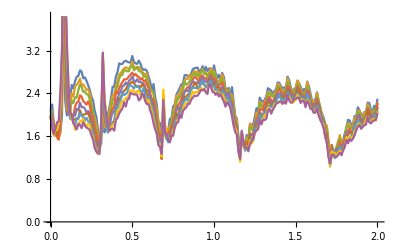

```mathematica
ListLinePlot[Table[Import["~/PhD_new/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/size_"<>ToString[10]<>"_asy_"<>ToString[x]<>"_.dat"],{x,Range[5,45,5]}]]
```

```mathematica
Dimensions[transmission[[1,2]]]
```

{201,2}

```mathematica
misfit[x_,y_,n_,area_]:=Module[{m5=input[[n]]},
ρ1=Table[{area,transmission[area][[con,1]],Module[{B1=Transpose[{m5[[1;;201]][[;;,1]],(m5[[1;;201,2]]-transmission[area][[con,2]][[1;;201,;;]][[;;,2]])^2}]},NIntegrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]},{con,9}];lista=ρ1;
{lista,lista[[Position[lista,Min[lista]][[1,1]]]]}]
```

```mathematica
Clear[a]
```

```mathematica
a[n_,area_]:=a[n,area]=Table[{x,Interpolation[misfit[2,0,n,area][[1]]][x]},{x,5,45,1}]
```

```mathematica
y[n_,area_]:=a[n,area][[Position[a[n,area],Min[a[n,area]]][[1,1]]]][[1]]
```

```mathematica
abc=Table[Join[(*misfit[2,0,n,10][[1]],*)misfit[1,0.15,n,10][[1]],(*misfit[2,0,n,15][[1]],*)misfit[1,0.15,n,20][[1]]],{n,50}]
```

```mathematica
cba=Table[abc[[x]][[Position[abc[[x]],Min[abc[[x]]]][[1,1]]]],{x,50}]
```

{{10,40,0.02244},{10,30,0.0109659},{10,25,0.0110019},{10,45,0.0223199},{20,45,0.00488537},{10,40,0.0185087},{10,45,0.00745955},{10,45,0.0146532},{20,10,0.00593871},{10,5,0.00520154},{10,45,0.00723159},{20,40,0.00909655},{20,40,0.00929487},{20,40,0.00751444},{20,40,0.00732671},{10,30,0.00877276},{10,25,0.00513717},{20,45,0.00969651},{10,40,0.0149433},{10,40,0.0124703},{20,45,0.0160606},{10,40,0.0197433},{20,25,0.00919992},{10,45,0.0110757},{20,10,0.00570853},{10,15,0.00599759},{20,45,0.0188332},{20,20,0.00570084},{10,35,0.0164844},{10,35,0.00919973},{10,30,0.0122517},{10,45,0.00969165},{10,45,0.00870339},{10,45,0.00876689},{10,35,0.00770249},{10,45,0.00565843},{20,40,0.00535415},{10,20,0.00789673},{10,45,0.00618752},{20,35,0.0135647},{10,45,0.0107247},{10,30,0.0192985},{20,15,0.00824966},{20,20,0.00498596},{20,45,0.00652437},{20,10,0.00412672},{10,20,0.00835618},{10,45,0.00820537},{10,40,0.0135749},{10,35,0.00537035}}

```mathematica
Mean[Abs[Transpose[cba][[2]]-35]]/35
```

48/175

```mathematica
Table[a[n,5][[Position[a[n,5],Min[a[n,5]]][[1,1]]]][[1]],{n,20}]
```

```mathematica
Abs[Table[a[n,5][[Position[a[n,5],Min[a[n,5]]][[1,1]]]][[1]],{n,20}]-10]/10//Mean
```

3/5

```mathematica
Abs[Table[a[n,10][[Position[a[n,10],Min[a[n,10]]][[1,1]]]][[1]],{n,20}]-10]/10//Mean
```

71/100

```mathematica
N[12/25]
```

0.48

```mathematica
N[167/700]
```

0.238571

```mathematica
Abs[Table[misfit[2,0.15,n][[2]][[1]],{n,20}]-35]/35//Mean
```

8/35

```mathematica
N[8/35]
```

0.228571

```mathematica
N[9/35]
```

0.257143

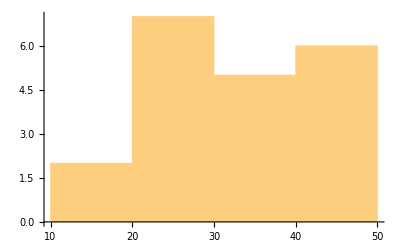

```mathematica
Table[misfit[1.5,0,n][[2]][[1]],{n,20}]//Histogram
```

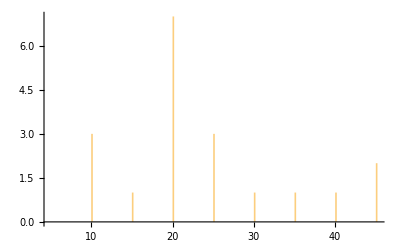

```mathematica
Histogram[{20,20,5,45,25,10,20,20,40,35,15,45,20,20,20,10,10,25,25,30},{0.2}]
```